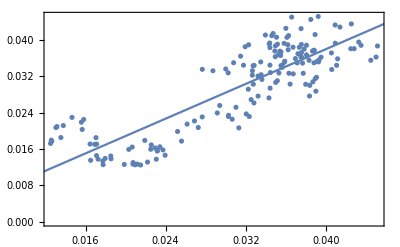

```mathematica
SetDirectory["G:\\git\\manchesterCS\\61011\\project"];
tryAR1$179=Import["g:/git/manchesterCS/61011/alenaMatlabCode/aBunch/ AR(1)TheTry$179$.mat"];


trycurve251=Import["g:/git/manchesterCS/61011/alenaMatlabCode/aBunch/ US curvatureTheTry$251$.mat"];

forLFit=ArrayFlatten[{{tryAR1$179[[1]],tryAR1$179[[2]]}}];

model=LinearModelFit[forLFit,xx,xx];

Show[lp=ListPlot[forLFit],Plot[model[xx],{xx,0,5}],Frame->True,DisplayFunction->$DisplayFunction]
```

```mathematica
aFew=Range[165];

allX=Transpose[forLFit[[All,{1}]]];
allY=forLFit[[All,2]];
tryX=allX[[All,aFew]];
tryY=allY[[aFew]];

aFew=Range[20];
allCX=Transpose[trycurve251[[1,All,{1,2}]]];
allCY=Flatten[Transpose[trycurve251[[2,All]]]];
tryCX=allCX[[All,aFew]];
tryCY=allCY[[aFew]];
```

```mathematica
svmt=JavaNew["libsvm.trainGuts"];
svmt[mmaUreadUproblemPoly[Transpose[allCX],Flatten[allCY],{100,.001,10,.2,1}]];svmDoer=JavaNew["libsvm.svm"];
mod=svmDoer[svmUtrain[svmt[prob],svmt[param]]];svind=mod[svUindices];
```

```mathematica
some=svmDoer[svmUpredict[mod,#]]&/@Transpose[allCX][[svind]];
```

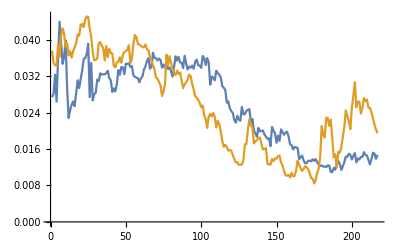

```mathematica
ListLinePlot[{some,allCY[[svind]]}]
```

```mathematica
all=svmDoer[svmUpredict[mod,#]]&/@Transpose[allCX];
```

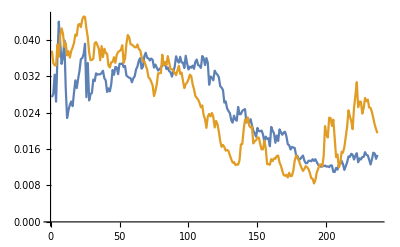

```mathematica
ListLinePlot[{all,allCY}]
```

```mathematica
svmDoer[svmUcrossUvalidation[svmt[prob],svmt[param], 3, Table[0,{237}]]]
```

```mathematica
mod
```

«JavaObject[libsvm.svm_model]»

```mathematica
Fields[mod]
```

int l
[I label
int maxIndex
int nr_class
[I nSV
libsvm.svm_parameter param
[D probA
[D probB
[D rho
[[Llibsvm.svm_node; SV
[[D sv_coef
[I sv_indices
[[D theValueMatrix

```mathematica
hip=mod[theValueMatrix];
```

```mathematica
Dimensions[hip]
```

{132,13}

```mathematica
mod[SVtoMatrices[]]
```

```mathematica
haa=mod[SV];
```

```mathematica
haa[[1,1]][value]
```

0.166667